```mathematica
GrowVP[V_,T_,Core_]:=Module[{currentVolume,remainingTime,remainingVolume,maxBoundaryVolume,possibleBoundaryVolumes,remainingDoubles,remainingSingles},currentVolume=2*Total[Core];
remainingTime=T-Length[Core];
remainingDoubles=remainingTime-2;
remainingSingles=2;
remainingVolume=V-currentVolume;
maxBoundaryVolume=remainingVolume-(remainingDoubles*2)-remainingSingles;
isNotFinalBoundary=If[remainingDoubles==0,0,1];
maxBoundaryLength=maxBoundaryVolume/(1+isNotFinalBoundary);
possibleBoundaryLengths=If[remainingDoubles==0,{maxBoundaryLength},Table[i,{i,0,maxBoundaryLength}]];
possibleBoundarys=Flatten[Table[Table[{i,L-i}+{1,1},{i,0,L}],{L,possibleBoundaryLengths}],1];
Table[{b[[1]]}~Join~Core~Join~{b[[2]]},{b,possibleBoundarys}]]
AllVP[V_,T_,currentList_]:=If[Length[currentList[[1]]]!=T,AllVP[V,T,Flatten[Table[GrowVP[V,T,vp],{vp,currentList}],1]],currentList]
AllVP[V_,T_]:=AllVP[V,T,{{}}];
W[vp_]:=Product[Binomial[vp[[i]]+vp[[i+1]],vp[[i]]],{i,Length[vp]-1}];
Flatten[Table[GrowVP[10,4,vp],{vp,GrowVP[10,4,{}]}],1]
TotalMultiplicity[V_,T_,Core_]:=Sum[W[vp],{vp,AllVP[V,T,{Core}]}]
```

{{1,1,1,5},{2,1,1,4},{3,1,1,3},{4,1,1,2},{5,1,1,1},{1,1,2,3},{2,1,2,2},{3,1,2,1},{1,2,1,3},{2,2,1,2},{3,2,1,1},{1,1,3,1},{1,2,2,1},{1,3,1,1}}

{{14,Log[4306]/(14 Log[2])},{15,Log[10526]/(15 Log[2])},{16,Log[29302]/(16 Log[2])},{17,Log[68150]/(17 Log[2])},{18,Log[171518]/(18 Log[2])},{19,Log[385520]/(19 Log[2])},{20,Log[911706]/(20 Log[2])},{21,Log[1999818]/(21 Log[2])},{22,Log[4538170]/(22 Log[2])},{23,Log[9776664]/(23 Log[2])},{24,Log[21558112]/(24 Log[2])},{25,Log[45813462]/(25 Log[2])},{26,Log[98950008]/(26 Log[2])},{27,Log[208071800]/(27 Log[2])},{28,Log[442550182]/(28 Log[2])},{29,Log[922893240]/(29 Log[2])},{30,Log[1940178170]/(30 Log[2])},{31,Log[4019289750]/(31 Log[2])},{32,Log[8374047122]/(32 Log[2])},{33,Log[17254970342]/(33 Log[2])},{34,Log[35697908410]/(34 Log[2])},{35,Log[73235109156]/(35 Log[2])},{36,Log[150668699914]/(36 Log[2])},{37,Log[307986452174]/(37 Log[2])},{38,Log[630799157780]/(38 Log[2])},{39,Log[1285573225922]/(39 Log[2])},{40,Log[2623507296462]/(40 Log[2])}}

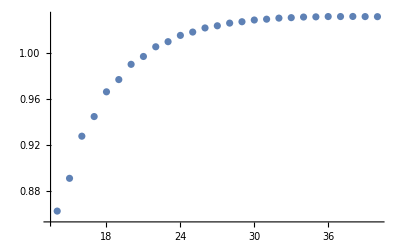

```mathematica
dataX = Table[V,{V,14,40}];
data = Table[{V,Log[2,TotalMultiplicity[V,6,{}]]/V},{V,dataX}]
ListPlot[data]
```

```mathematica
{a->3.1896618788452265,b->1168.792595521957,c->2.7906262821016043,d->1.,e->1.}
```

{a→1.99553,b→289.665,c→2.62557,d→1.,e→1.}

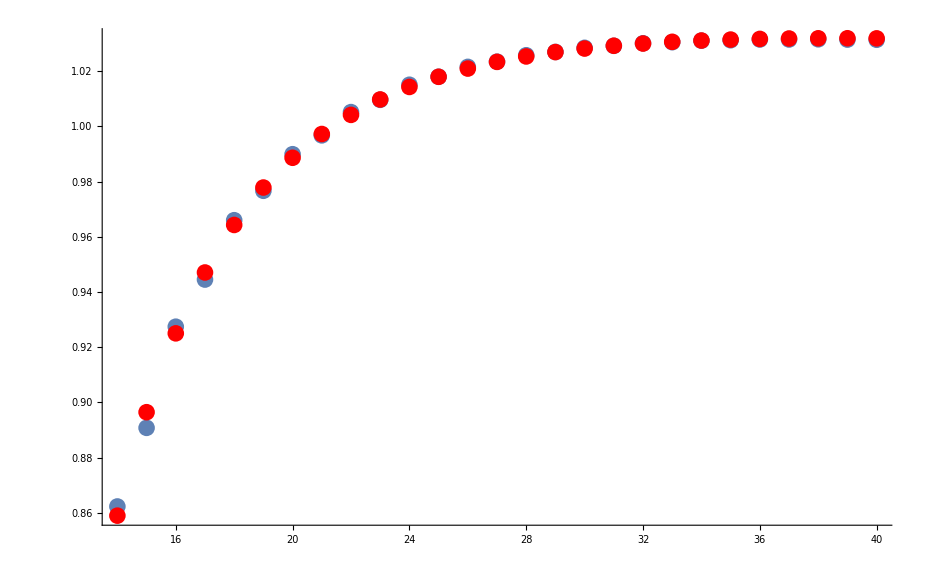

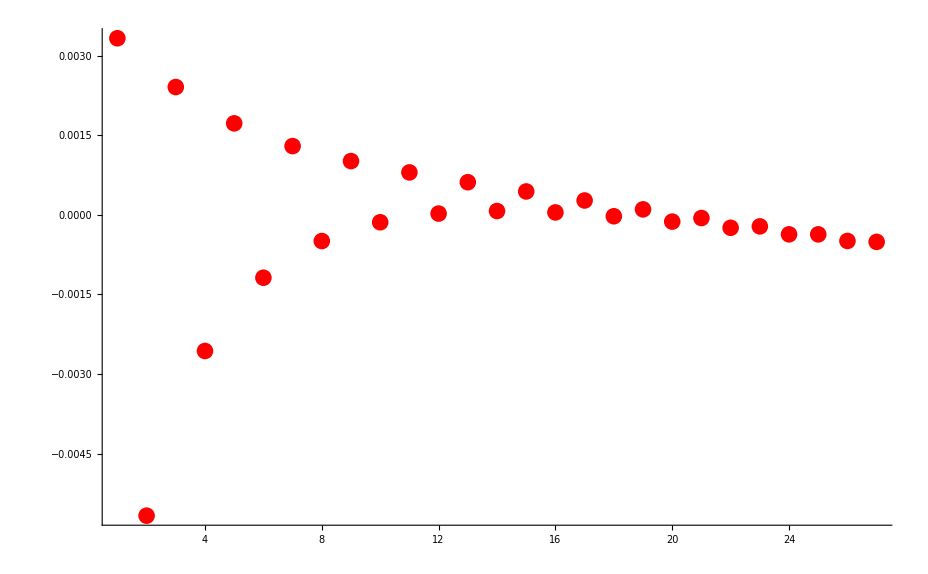

```mathematica
model[x_]:=-b/x^c+a/x+1
fit=NonlinearModelFit[data,model[x],{a,b,c,d,e},x];
fit["BestFitParameters"]
Show[ListPlot[data],ListPlot[Table[{x,fit[x]},{x,Min[dataX],Max[dataX]}],PlotStyle->Red],PlotRange-> All]
Show[ListPlot[fit["FitResiduals"],PlotStyle->Red],PlotRange-> All]
```